```mathematica
GiniCoefficient[data_List]:=Module[{n=Length[data],mean,diffSum},mean=Mean[data];
diffSum=Total[Flatten[Abs[#1-#2]&@@@Tuples[data,2]]];
diffSum/(2 n^2 mean)];
Do[
Sglist={};
grlist={};

model1=10^(Log10[80]+(Log10[1600]-Log10[80])*Exp[-Exp[x0*(t-dx)]]);
model2=80+x0*t;
model3=80*Exp[x0*t];
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],"motile-QS","Para"<>ToString@i,"mot"<>ToString@j,"celldata"}]];
cellfile=FileNames[];
time=Sort@Table[ToExpression@StringDrop[StringDrop[cellfile[[k]],10],-4],{k,1,Length@cellfile}];
cellcount={};
Do[
celldata=Import[FileNameJoin[{NotebookDirectory[],"motile-QS","Para"<>ToString@i,"mot"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[k]]<>".csv"}]];
cellnum=Length@celldata;
cellcount=Join[cellcount,{cellnum}];
,{k,1,Length@time}];
Sg=60*Flatten@Take[celldata,All,{-1}];
Sgmean=Mean@Sg;
Gini=GiniCoefficient[Sg];
Sglist=Join[Sglist,{{Sgmean,Gini}}];

fitcount=Transpose@Join[{time},{cellcount}];
fit=NonlinearModelFit[fitcount,model2,{x0},t];
Mumax=(x0/.fit["BestFitParameters"])*60/800;(*h-1*)
(*fit=NonlinearModelFit[fitcount,model,{x0,dx},t];
fasttp=dx/.fit["BestFitParameters"];
Mumax=fit'[fasttp];*)
grlist=Join[grlist,{Mumax}];
If[Divisible[j,5]==True,Print["Para No."<>ToString@i<>" mot No."<>ToString@j<>" finished!"]]
,{j,1,30}];
Export[FileNameJoin[{NotebookDirectory[],"data","Popgro-"<>ToString@i<>".csv"}],grlist];
Export[FileNameJoin[{NotebookDirectory[],"data","Cellgro-"<>ToString@i<>".csv"}],Sglist];
,{i,5,5}];
```

Para No.5 mot No.5 finished!

Para No.5 mot No.10 finished!

Para No.5 mot No.15 finished!

Para No.5 mot No.20 finished!

Import::fmterr: 无法将数据以 ZIP 格式导入.

General::stop: 在本次计算中，Import::fmterr 的进一步输出将被抑制.

Take::normal: Take[$Failed,All,{-1}] 中的位置 1 处应该是非原子表达式.

Para No.5 mot No.25 finished!

Para No.5 mot No.30 finished!

```mathematica
popdata=Table[Flatten@Import[FileNameJoin[{NotebookDirectory[],"data","Popgro-"<>ToString@i<>".csv"}]],{i,1,10}];
Show[ListPlot[popdata,ImageSize->1000,AspectRatio->0.75,PlotRange->{{-2,52},{-0.2,2.5}},
PlotStyle->Directive[PointSize[0.01],ColorData[95]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,48],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,2.5,0.5],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}],
ListLinePlot[popdata,ImageSize->1000,AspectRatio->0.75,PlotRange->{{-2,52},{0,2.5}},
PlotStyle->Directive[Thickness[0.0025],ColorData[95],Dashing[0.0075]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,48],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,2.5,0.5],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}]];
```

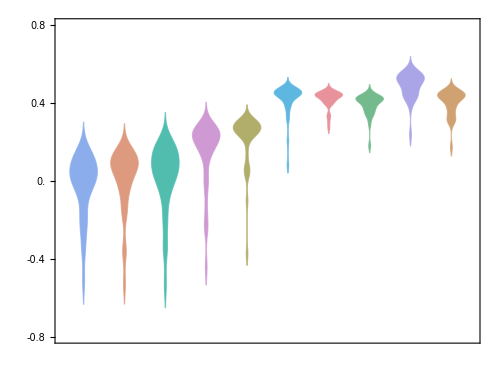

```mathematica
popbase=Flatten[Import[FileNameJoin[{NotebookDirectory[],"data","Popgro-base.csv"}]]];
popbase1=Transpose[Table[popbase,30]][[1;;10]];
popdata1=Log10[popdata/popbase1];
DistributionChart[popdata1,ImageSize->500,AspectRatio->0.75,PlotRange->{{0.5,10.5},{-0.8,0.8}},
ChartStyle->ColorData[95],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[-0.8,0.8,0.4],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}]
```

TTest::nortst: {0,0.0294122} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

TTest::nortst: {0.000171907,0.000501141} 中至少有一个通过正态性检验得到的 p 值低于 0.025. {T} 中的检验要求数据服从正态分布.

{0.38101,0.749033,0.960323,0.00720019}

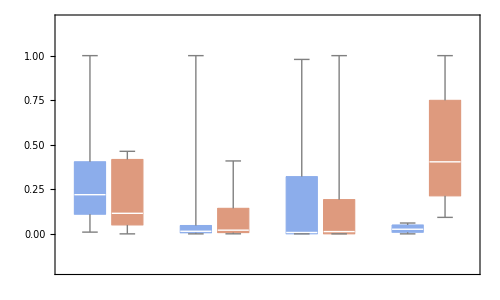

```mathematica
group1=Select[popdata1,Min[#]<0&];
group2=Select[popdata1,Min[#]>0&];
pos1=Flatten@Table[Position[popdata1,group1[[i]]],{i,1,Length@group1}];
pos2=Flatten@Table[Position[popdata1,group2[[i]]],{i,1,Length@group2}];
para1=Table[paraset1[[pos1[[i]]]],{i,1,Length@pos1}];
para2=Table[paraset1[[pos2[[i]]]],{i,1,Length@pos2}];
Sigtest=Table[TTest[{Transpose[para1][[i]],Transpose[para2][[i]]}],{i,1,4}]
BoxWhiskerChart[Table[Join[{Transpose[para1][[i]]},{Transpose[para2][[i]]}],{i,1,4}],ImageSize->500,AspectRatio->0.6,PlotRange->{-0.2,1.2},BarSpacing->{0.2,1},
ChartStyle->ColorData[95],ChartBaseStyle->EdgeForm[Thick],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,24],Axes->False]
```

```mathematica
paraset11=Import[FileNameJoin[{NotebookDirectory[],"paraset.csv"}]];
SortBy[paraset11,Last][[12]]
```

{0.905,8.97×10^-7,0.08671,0.04279}

{{-0.296999,-0.407827,-0.56072,-0.181273,-0.158703,-0.53383,-0.581945,-0.173878,-0.0419208,-0.470444,-0.432029,-0.448451},{-0.546218,-0.39976,-0.648691,-0.365666,-0.277983,-0.581176,-0.65599,-0.313037,-0.303914,-0.477839,-0.584826,-0.626699},{0.529028,0.517983,0.287011,0.542089,0.675198,0.395438,0.282497,0.70401,0.599232,0.437215,0.466699,0.3891}}

{{0.0362156,0.00328403,0.0000228361,0.207728,0.270978,0.0000654241,9.30608×10^-6,0.227191,0.77254,0.000565729,0.00173051,0.00109012},{0.0000407379,0.00402467,3.49654×10^-7,0.00901792,0.050626,9.62404×10^-6,2.32484×10^-7,0.0268646,0.0318987,0.000449234,8.19824×10^-6,1.12264×10^-6},{0.0000782244,0.000116805,0.0432923,0.0000478055,7.52018×10^-8,0.00447889,0.0468423,1.17226×10^-8,4.2699×10^-6,0.00149922,0.000634562,0.0052263}}

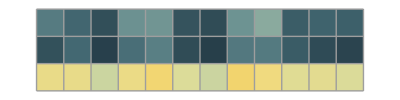

{{-0.299411,-0.318984,-0.373699,-0.198863,-0.197454,-0.47641,-0.435765,-0.290381,-0.231907,-0.316855,-0.385866,-0.374438},{-0.431424,-0.385254,-0.516192,-0.226065,-0.288654,-0.51386,-0.624406,-0.331367,-0.27349,-0.422863,-0.522895,-0.527025},{0.369883,0.400921,0.295282,0.341114,0.347433,0.404472,0.336149,0.420338,0.339562,0.341535,0.427933,0.370868}}

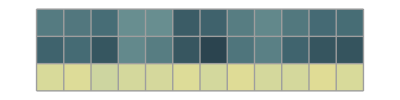

```mathematica
paraset2=Import[FileNameJoin[{NotebookDirectory[],"paraset2.csv"}]];
paraset2=ToExpression@Transpose@Table[Rescale@Flatten@Take[paraset2,All,{i}],{i,1,3}];
fitlist={};
spearmanlist1={};
spearmansig1={};
Do[fitdata=Transpose@Join[Transpose@paraset2,{Rescale@group1[[i]]}];
fitmodel=LinearModelFit[fitdata,{x1,x2,x3},{x1,x2,x3}];
fitmodel["AdjustedRSquared"];
fitlist=Join[fitlist,{fitmodel["BestFitParameters"][[2;;4]]}];

spearmanlist1=Join[spearmanlist1,{{SpearmanRho[Flatten@Take[paraset2,All,{1}],Rescale@group1[[i]]],SpearmanRho[Flatten@Take[paraset2,All,{2}],Rescale@group1[[i]]],SpearmanRho[Flatten@Take[paraset2,All,{3}],Rescale@group1[[i]]]}}];
spearmansig1=Join[spearmansig1,{{SpearmanRankTest[Flatten@Take[paraset2,All,{1}],Rescale@group1[[i]]],SpearmanRankTest[Flatten@Take[paraset2,All,{2}],Rescale@group1[[i]]],SpearmanRankTest[Flatten@Take[paraset2,All,{3}],Rescale@group1[[i]]]}}];
,{i,1,Length@group1}];
Transpose@spearmanlist1
Transpose@spearmansig1
spearplot=Table[ColorData["StarryNightColors"][Rescale[Transpose[spearmanlist1][[i,j]],{-0.8,0.8}]],{i,1,3},{j,1,Length@spearmanlist1}];
MatrixPlot[spearplot,Mesh->All,Frame->False]

Transpose@fitlist
spearplot=Table[ColorData["StarryNightColors"][Rescale[Transpose[fitlist][[i,j]],{-0.8,0.8}]],{i,1,3},{j,1,Length@fitlist}];
MatrixPlot[spearplot,Mesh->All,Frame->False]
```

```mathematica
QSlist={5,10,25,50,100,150,200,300,700,1000};
QSlist1={"5","10","25","50","100","150","200","300","700","1000"};
gElist={0.005,0.0075,0.01,0.025,0.05,0.075,0.1,0.2,0.3,0.4};
plotlist={};
thresist={};
Do[
popdata=Table[Flatten@Import[FileNameJoin[{NotebookDirectory[],QSlist1[[i]],"data","Popgro-"<>ToString@j<>".csv"}]],{j,1,10}];
popbase=Flatten[Import[FileNameJoin[{NotebookDirectory[],QSlist1[[i]],"data","Popgro-base.csv"}]]];
popbase1=Transpose[Table[popbase,30]][[1;;10]];
popdata1=Log10[popdata/popbase1];
varadata=Select[popdata1,Min[#]<0&];
varapos=Flatten@Table[Position[popdata1,varadata[[i]]],{i,Length@varadata}];
thres=gElist[[Max@varapos+1]];
thresist=Join[thresist,{thres}];
plot=DistributionChart[popdata1,ImageSize->100,AspectRatio->0.75,PlotRange->{{0.5,10.5},{-0.8,0.8}},
ChartStyle->ColorData[95],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,14],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[-0.8,0.8,0.4],None},{{#,#,{0.02,0}}&/@Range[0,50,10],None}}];
plotlist=Join[plotlist,{plot}];
,{i,1,10}];
fitdata=N@Log10@Transpose@Join[{QSlist},{thresist}]
fit=LinearModelFit[fitdata,x,x]
plot1=Show[Plot[fit[x],{x,0.5,3.5},ImageSize->300,AspectRatio->1,PlotRange->{{0.5,3.5},{-2.5,0}},PlotStyle->Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[-2.5,0,0.5],None},{{#,#,{0.02,0}}&/@Range[0.5,3.5,1],None}}],ListPlot[fitdata,PlotStyle->Directive[PointSize[0.025],RGBColor[126/255,132/255,195/255]]]]
fit["AdjustedRSquared"]
Export[FileNameJoin[{NotebookDirectory[],"plot","growth-thres-corr.eps"}],plot1]
```